# NEWTON’S LAWS

## Lab Report

Names: Aryan Malhotra
Section: H4
Date: 9/25/24

## Purpose

To understand the concepts of Newton’s Laws of motion.
To learn about the linear fitting and the least-squares fitting method.

## Readings

### Books & References

Chapter 8 of John R Taylor's book talks about least-squares fitting which we will use in this lab to do linear fitting and calculate the errors.
Also section 2.6 talks about checking relationships with graphs.
You can learn more about coefficient of linear correlation in section 9.3.
To learn more about Newton’s Laws check out your favorite mechanics textbook.

### Introduction to Newton’s Laws

In the late 1600’s Isaac Newton formulated the three fundamental laws of motion:
1. Every object continues in its state of rest or of uniform speed in a straight line unless it is compelled to change that state by a net force acting on it.
2. The acceleration of an object is directly proportional to the net force acting on it and is inversely proportional to its mass. The direction of the acceleration is in the direction of the applied net force.
3. When one object exerts a force on a second object, the second object exerts an equal and opposite force on the first.

The First Law is not intuitively obvious from everyday experience. Friction, an unseen force, slows things down. Early philosophers, followers of Aristotle, taught that everything naturally tended to slow down and come to rest even without a force.

The Second Law is essentially the equation F = ma. Note that it describes the net force; there can be more than one force in many instances. Their vector sum is the net force. The Aristotelians got this law wrong too. They assumed that velocity, not acceleration, was proportional to force. 

The Third Law is that every force (or action) is accompanied by an opposite force: F1 = −F2 or F1 + F2 = 0. That is, you push on something and you feel an opposite (and equal) force. Note that the First and Second Laws refer to a single object while the Third Law is about two interacting objects. In this lab we will do several exercises to verify the Second Law.

### A Short Review of Least-Squares Fitting

Say we want to investigate the relation between two physical variables x and y. We have a theory that says y = Bx + A where B and A are some constants in the theory. We have measured a set of (x_i,y_i) pairs, meaning that for each x_i we also measured the corresponding y_i. So we have x_1, ..., x_N and the corresponding y_1, ..., y_N, i.e. total of N data points. We want to estimate the parameters A and B using these data points.

Doing the prerequisite, you have learned that this is called linear fitting and the correlation coefficient shows how well x and y are linearly correlated, i.e. satisfy y = Bx + A. Now, the most usual way to estimate A and B is to minimize the sum of squares of residuals, also known as least-squares fitting,
S=∑_(i=1)^N r_i^2=∑_(i=1)^N (y_i-B x_i-A)^2.
The residuals r_ishow how far a point y_i sits from the value (ŷ)_i=B x_i+A which linear model estimates. By minimizing these residuals, using two degree of freedom B and A, we make the data points closer to a line.

As a side note, remember that the least-squares is the most usual way of doing linear fitting as it gives us a simpler linear problem to solve. This is not true if we consider summing the absolute values, |y_i-(ŷ)_i|, or forth powers, (y_i-(ŷ)_i)^4,  instead of squares.

By setting the derivatives ∂/(∂A)S and ∂/(∂B)S to zero, we get two linear equations which can be solved for A and B,
Â = (∑x^2∑y- ∑x∑xy)/Δ,
B̂=(N∑xy-∑x∑y)/Δ,
Δ=N∑x^2-(∑x)^2.
Above we have dropped the indices for convenience in writing. And the hat above A and B means these are the estimation based on over data.
After finding an estimation for the slope, B̂ above, and an estimation for the intercept, Â above, one might wonder how much error this fitting has, in other words what is σ_A and σ_B when we report over estimations,
A=Â ± σ_A, B=B̂± σ_B.
Here, I only copy the formulas,
σ_y=√(1/(N-2)∑_(i=1)^N (y_i-B̂ x_i-Â)^2),
σ_A=σ_y √((∑_(i=1)^N x_i^2)/Δ),
σ_B=σ_y √(N/Δ).
For a sketch of derivation of the above formulas, take a look at the sections 8.3 and 8.4 of the John R. Taylor's.
Sometimes we drop the hats in the notation above as we know based on the context that we are talking about the estimation using data.

### Some References to Mathematica Commands

ErrorListPlot

## Procedure

In the first part of the lab you will first use the data acquisition program LoggerPro to measure the gravitational force exerted on the force probe by different masses.
In the second part you verify Newton’s second law for an oscillating object.

### Setting Up the Data Collection Program LoggerPro

- Attach the force probe to the overhead bracket and hang the mass hanger (two pieces) from it.
- Make sure that the button on the back of force probe is set to ±10N.
- Load the computer program LoggerPro by double clicking on its icon.
- Add the force detector  by clicking on the Vernier icon , and then clicking on the CH1⇒ Choose Sensor ⇒ force ⇒ Dual Range Force
-Graphics-

- Next click on the Dual Range Force icon⇒Change Sensor Range and make sure the range of Force probe is set to ±10 N. -Graphics-
- Zero the force probe by clicking zero icon. -Graphics-

- Click on the clock icon.   Set the data collection rate to 30 Hz.    -Graphics-

- For the second part, add the motion detector by clicking on the Vernier icon ,
and then clicking on  Dig/SONIC1⇒ Choose Sensor ⇒ Motion Detector

-Graphics-

### Force Calibration

Before calibrating, do a short run with a small mass (50 g) on the holder.  If the force remains exactly constant or does not show up,  you will have to deselect the force in the sensor setup menu, then reload it and start again.  The calibration does not work properly if you calibrate before doing one run.  To calibrate the probe, first put on only the holder.

1. On the menu go to Experiment > Set Up Sensors > Show All Interfaces (or click on the Vernier icon ).
2. Click on CH 1, where the force sensor is attached.
3. Click on Calibrate. A window Sensor Settings will pop up.
4. Click on Calibrate Now.
Now you can edit the text box “Reading 1”.
The force sensor is “intrinsically” measuring a voltage which is proportional to the force. This voltage is written in the middle. We want to map this voltage to the correct force.
5. With only the mass hanger insert 0 (N) in Reading 1 and Click on Keep.
6. Now you can edit Reading 2. Now put on some mass (250 g) and enter the additional force in Newtons for Reading 2 (i.e., 0.250*9.81 = 2.453 (N), so insert 2.453 and  do not include the mass of holder). Click on Keep.

The probe should now be calibrated. From time to time take off the weights (mass hanger remains) and select Zero and then Zero Force.
Although the calibration remains good, the zero offset for force tends to drift, so check it often.

## Dialog:

## Part I. Newton’s Second Law - Static Equilibrium

#### In this part you measure the acceleration of gravity g.

If you fix the force probe in a clamp and hang a mass from it, there are two forces acting on the hook of the probe; the weight W of the mass acting down and the upward pull P of the probe. Since the probe is clamped, there is no acceleration and Newton’s second law tells us that W+P = 0. What we call the weight of the mass is the force of gravitational attraction by the earth and is proportional to the mass, W ∝ m. Or letting the constant of proportionality be g, W = mg. We call g the acceleration of gravity. [This is a little confusing since there is no acceleration. What we mean is if the mass were dropped then only W would act on the mass and by the Second Law W = mg = ma or a = g. Thus g is the acceleration a body would experience due to the force of gravity if it were allowed to fall freely.] Then substituting into W+P = 0, we find P = mg.

In this part of today’s lab you will use the force probe to measure P using LoggerPro.
Then, you will import your data into Mathematica to plot your data and see whether P = mg as predicted by the Second Law.
Finally you will determine g from the slope of a graph of P versus m.

### Step 1. Setting up the Force probe and finding the uncertainty in the measurements

- While no extra mass is on the hanger zero the force probe as explained in the Procedure section.
- Put the 200 g mass on the hanger and start collecting data for a few seconds.
- Export your data in CVS format.
- Import your data into Mathematica file using Import[Insert/File Path...]
- Find the standard deviation of your force measurements. 
- Use this standard deviation as the uncertainty of your force measurements in this lab.
- Take 1g for the uncertainty in the mass values.

```mathematica
Needs["ErrorBarPlots`"];
f=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab3MeasurementUncertainty.csv"];
mu=Mean[Rest[Part[f ,All,2]]]
sigma=StandardDeviation[Rest[Part[f ,All,2]]]
```

1.9659

0.00545244

### Step 2. Measuring force vs mass

- Now, starting with only a small amount of mass measure and record the force (weight) on the probe. 
- Save the mass and measured force in the two columns below. (Notice that you need to save the mass values in Kg.) [you can use Insert Table from the top menu.]
- Do this for a range of masses up to a total of 150 to 200 g. 
- Be sure to include a mass of zero as one of your data points!

```mathematica
"--mass0--:"
f0=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt1Mass0.csv"];
mu0=Mean[Rest[Part[f0 ,All,2]]]

"mass150"
f150=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt1Mass150.csv"];
mu150=Mean[Rest[Part[f150,All,2]]]

"mass170"
f170=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt1Mass170.csv"];
mu170=Mean[Rest[Part[f170 ,All,2]]]

"mass190"
f190=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt1Mass190.csv"];
mu190=Mean[Rest[Part[f190 ,All,2]]]

"mass200"
f200=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt1Mass200.csv"];
mu200=Mean[Rest[Part[f200 ,All,2]]]
```

--mass0--:

-0.00076

mass150

1.47558

mass170

1.67238

mass190

1.86916

mass200

1.96532

```mathematica
fvm={{.0, 0.00}, {.15, 1.48}, {.17, 1.67}, {.19, 1.87}, {.20, 1.97}};
Grid[Prepend[fvm,{"Mass, Kg","Force, N"}], Frame -> All]
```

Mass, Kg | Force, N
0. | 0.
0.15 | 1.48
0.17 | 1.67
0.19 | 1.87
0.2 | 1.97

### Step 3. Plotting force vs mass and calculating g

- Find the linear fit to your data using Fit[data,{1,x},x].  
- Plot your data with the error bars using ErrorListPlot[]. Include uncertainty and 5% of calibration error. 
- Plot your data and its linear fit together using Show[] command.

9.84471 x

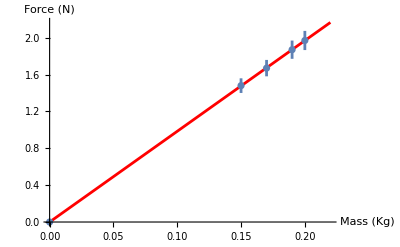

```mathematica
line=Fit[fvm, {x},x]
Show[Plot[line,{x,0,.22},PlotStyle->Red],ErrorListPlot[Join[fvm, Table[{sigma+0.05*fvm[[i]][[2]]},{i,1,Length[fvm]}], 2]], AxesLabel->{"Mass (Kg)","Force (N)"}]
```

#### Question 1: Report your value of g with its error. The way to estimate the error of the slope, when doing a least squares fitting, is covered above in the Readings section.

Δ=N∑x^2-(∑x)^2
σ_B=σ_y √(N/Δ)
y=Bx+A
Force = B(mass)+A

Considering that our variations for all values of data points are similar, I use mu and sigma calculated from dataset f for the following calculations of my variations that the variation of the final value B relies on.

```mathematica
n=Length[f]-1 (* 1 of the elements is the header row *)
delta =(Sum[n*((f[[i]][[1]])^2), {i, 2, n}]-(Sum[(f[[i]][[1]]), {i, 2, n}])^2)
sigmaY =StandardDeviation[Rest[Part[fvm ,All,2]]]
sigmaB = sigmaY * Sqrt[n/delta]
```

300

748492.

0.21762

0.00435677

The Approximate Value of g calculated is 9.84 ± 0.004 m/s^2.

## Part II. Newton’s Second Law - Accelerated Motion

#### We will now verify Newton’s Second Law for a case where the acceleration is not zero - a mass oscillating up and down due to the pull of a spring.

### Step 1. Measuring Force vs Acceleration for oscillating mass

- Attach the spring and hanger to the force probe and add about 150 g of additional mass. 
- Place the motion sensor on the table beneath the weight.
- Activate the motion detector as explained in Procedure section.
- Set the mass oscillating and record data for 10 sec. 
- Save your data in CVS format and Import it into Mathematica.

### Step 2. Doing a linear fit and discussing the result

- Plot the data along with a linear fit to data. 
- Explain the result. 
- Prepare a graph of force vs. acceleration and fit the data to a straight line as you did for Part I. 
- What slope do you expect? 
- Explain slope’s relation to the Newton’s Second Law.

1.46694+0.297611 x

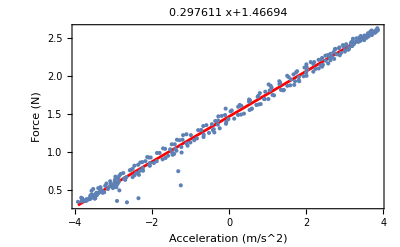

```mathematica
data=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt2OscillatingMass150.csv"];
(* you can check all your data by the command 
data data //TableForm *)
fva=Rest[Part[data, All,{5,2}]]; 
(* Part command takes the fifth, "Acceleration", and second, "Force", columns; 
Rest comand removes the title line *)
line2=Fit[fva, {1,x},x] (* Fit finds the best linear fit to the fva variables *)
Show[Plot[line2,{x,Min[Part[fva, All,1]],Max[Part[fva, All,1]]},PlotRange -> All, PlotStyle->Red, PlotLabel-> line2],ListPlot[fva], Frame->True, FrameLabel->{"Acceleration (m/s^2)","Force (N)"}]
```

It can be seen in the plot that Force vs Acceleration plot has a near linear fit. That means Force is linearly Proportional to Acceleration.
Since the mass for the oscillation experiment is a constant, we expect the slope of the graph (which must be the mass) to be constant.

Although the mass we add to the hanger is 150g, the hanger and the sprint themselves weights about 150g. Hence, the slope must be around 0.3kg Which is close to the actual slope 0.299.

Newton’s Law F=ma says If mass is constant, acceleration must have a linear relation with F which is exactly what we see in the plot. Hence, we can verify Newton’s 2nd law through the experiment.

### Step 3. Calculate the correlation coefficient R for the linear fit and explain its meaning (see your homework). Also calculate R^2.

```mathematica
(* you can use the command
LinearModelFit[fva,{1,x}, x]["RSquared"]
to check your result *)
RSquared = LinearModelFit[fva,{1,x}, x]["RSquared"]
r = Sqrt[RSquared]
```

(Since we can see from the data that the Force increases with an increase in mass, it is safe to assume that the correlation coefficient is positive.)

The correlation coefficient, measured in this case as the value 0.996, is a measure of how well a certain data set fits as described by a linear relation. It is valued -1 to 1. 
r = -1 means the relation is that of a perfect linear but negative curve (one function increases, the other decreases)
r = 0 means there seems to be absolutely no relation between our 2 variables in a dataset. (It happens to be zero in the limit of infinite measurements, in which case all variations would cancel out for the sum (x̄-x_i)(ȳ-y_i))
r = 1 means there is a perfectly linear and positive relation between the two variables in our datasets.

As for our correlation coefficient, it is extremely close to 1, confirming the linear relation of Force with the mass, as determined by Newton’s law F=ma.

0.992081

0.996033

### Step 4. Testing the Aristotelian prediction

- Make a similar plot for Force vs. Velocity.  
- Calculate the correlation coefficient for Force vs. Velocity and compare it to the correlation coefficient for Force vs. Acceleration above.

1.47274+0.139439 x

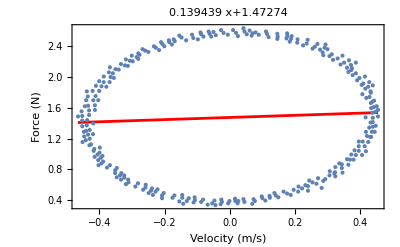

```mathematica
(* Use Part command to take the 4th, "Velocity", and 2nd, "force", columns *)
fvv=Rest[Part[data, All,{4,2}]];
line3=Fit[fvv, {1,x},x] (* Fit finds the best linear fit to the fvv variables *)
Show[Plot[line3,{x,Min[Part[fvv, All,1]],Max[Part[fvv, All,1]]},PlotRange -> All, PlotStyle->Red, PlotLabel-> line3],ListPlot[fvv], Frame->True, FrameLabel->{"Velocity (m/s)","Force (N)"}]
```

- Does the Aristotelian prediction that velocity is proportional to force hold for an oscillating mass? Please explain your answer.

It is very obvious that The velocity is not proportional to the force for an oscillating mass. In fact, it’s not even a function of the force (it has multiple outputs mapped to the same input) and rather also depends on the position of the object.


Regardless to say, is is not a linear plot and hence, it is evident that the Aristotelian prediction was wrong for oscillatory motion of a particle.

### Step 5. Design and carry out experiments to answer the following questions: - Does the size of the mass affect the results? How? - Does the amplitude of oscillation affect the results? How?

- Support your answers with additional data and the graphs.
- If you think the size of the mass or the amplitude is related to a parameter that you measure, explore the relationship using other proper graphs and fittings.

2.43782+0.395305 x

250 grams mass:

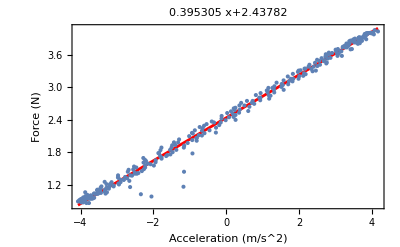

150 grams mass:

-Graphics-

```mathematica
dataOsc250=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt2OscillatingMass250.csv"];
(* you can check all your data by the command 
data data //TableForm *)
fva250=Rest[Part[dataOsc250, All,{5,2}]]; 
(* Part command takes the fifth, "Acceleration", and second, "Force", columns; 
Rest comand removes the title line *)
line4=Fit[fva250, {1,x},x] (* Fit finds the best linear fit to the fva250 variables *)

"250 grams mass:"
Show[Plot[line4,{x,Min[Part[fva250, All,1]],Max[Part[fva250, All,1]]},PlotRange -> All, PlotStyle->Red, PlotLabel-> line4],ListPlot[fva250], Frame->True, FrameLabel->{"Acceleration (m/s^2)","Force (N)"}]

"150 grams mass:"
Show[Plot[line2,{x,Min[Part[fva, All,1]],Max[Part[fva, All,1]]},PlotRange -> All, PlotStyle->Red, PlotLabel-> line2],ListPlot[fva], Frame->True, FrameLabel->{"Acceleration (m/s^2)","Force (N)"}]
```

As it can be seen from the curves, changing the mass does not change the relation between Force and Acceleration (except... the gradient). The Curve is still linear.
It does however mean that the slope of the curve increased since we increased the mass (by exactly 0.1 kg)(hence the proportionality constant). It also meant the initial force that our system had was higher (by exactly 0.1*g N)

(THE OSCILLATION MAGNITUDE WAS HELD CONSTANT FOR THE TWO EXPERIMENTS)

So yes, for different masses, Force is still linearly proportional to Acceleration.

Low Amplitude

1.47105+0.29483 x

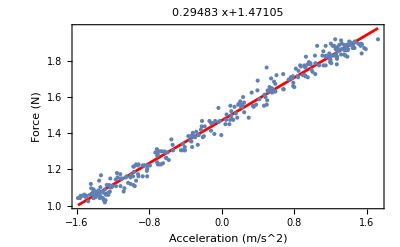

Mid Amplitude

-Graphics-

High Amplitude

1.45424+0.295609 x

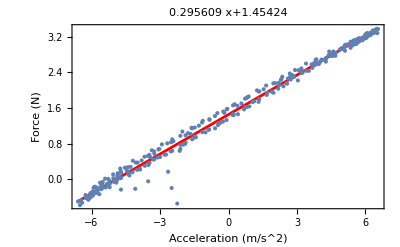

```mathematica
"Low Amplitude"
dataAmpLow=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt2OscillatingMass150LowAmp.csv"];
(*you can check all your data by the command data data//TableForm*)
fvaLow=Rest[Part[dataAmpLow,All,{5,2}]];
(*Part command takes the fifth,"Acceleration",and second,"Force",columns;
Rest comand removes the title line*)
lineLow=Fit[fvaLow,{1,x},x] (*Fit finds the best linear fit to the fva variables*)
Show[Plot[lineLow,{x,Min[Part[fvaLow,All,1]],Max[Part[fvaLow,All,1]]},PlotRange->All,PlotStyle->Red,PlotLabel->lineLow],ListPlot[fvaLow],Frame->True,FrameLabel->{"Acceleration (m/s^2)","Force (N)"}]

"Mid Amplitude"
Show[Plot[line2,{x,Min[Part[fva, All,1]],Max[Part[fva, All,1]]},PlotRange -> All, PlotStyle->Red, PlotLabel-> line2],ListPlot[fva], Frame->True, FrameLabel->{"Acceleration (m/s^2)","Force (N)"}]

"High Amplitude"
dataAmpHigh=Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Pt2OscillatingMass150HighAmp.csv"];
(*you can check all your data by the command data data//TableForm*)
fvaHigh=Rest[Part[dataAmpHigh,All,{5,2}]];
(*Part command takes the fifth,"Acceleration",and second,"Force",columns;
Rest comand removes the title line*)
lineHigh=Fit[fvaHigh,{1,x},x] (*Fit finds the best linear fit to the fva variables*)
Show[Plot[lineHigh,{x,Min[Part[fvaHigh,All,1]],Max[Part[fvaHigh,All,1]]},PlotRange->All,PlotStyle->Red,PlotLabel->lineHigh],ListPlot[fvaHigh],Frame->True,FrameLabel->{"Acceleration (m/s^2)","Force (N)"}]
```

The different Amplitudes do not vary the relation at all except they just change our range of data. So with a higher amplitude we get a higher range of values of Forces.

The Slope and intercept remains unchanged since the mass and acceleration due to gravity would remain unchanged (or rather, the latter is confirmed by the data). It is true however that with varying the amplitude, the variance in the data changes. With the low amplitude for instance, since the instrument had finite precision and mechanical errors were much more plausible, it was difficult to capture good data.

Rutgers 275 Classical Physics Lab
“Newton’s Laws”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014